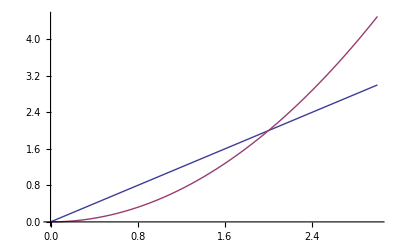

0 | 0
1 | 1/2
2 | 2
3 | 9/2
4 | 8

x^2/2

```mathematica
f[x_]:=x ;a:=0;
Φ[x_]=Limit[∑_(i=1)^n f[a+(i(x-a))/n](x-a)/n,n->∞];
Plot[{f[x],Φ[x]},{x,0,3}]
Table[{x,Φ[x]},{x,0,4}] //TableForm
Φ[x]
```

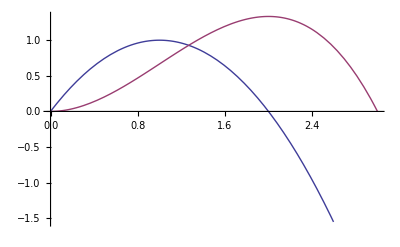

x^2-x^3/3

```mathematica
f[x_]:=2x-x^2 ;a:=0;
Φ[x_]=Limit[∑_(i=1)^n f[a+(i(x-a))/n](x-a)/n,n->∞];
Plot[{f[x],Φ[x]},{x,0,3}]
Φ[x]// Expand
```

```mathematica
Integrate[1/(x^2+1),{x,1,3}]
% // N
```

-π/4+ArcTan[3]

0.463648

```mathematica
∫_0^π Sin[3x]Cos[2x]ⅆx
```

6/5